## Functions

```mathematica
Py[ex_]:=ExportString[ex,"PythonExpression"]
```

```mathematica
ArrToStrPyOld[arr_]:="["<>StringTrim@StringJoin[", "<>ToString[#,InputForm]&/@arr]<>"]";
```

```mathematica
ArrToStrPy[arr_]:="["<>StringJoin[Table[ToString[arr⟦n⟧]<>If[n<Length[arr],", ",""],{n,1,Length[arr]}]]<>"]";
```

```mathematica
shAvgWrap[arr_]:=Module[{ln=Dimensions[arr]⟦1⟧,arr1d},
arr1d=Table[0,ln];
For[it=1,it≤ln,it++,
arr1d+=RotateLeft[arr⟦it⟧,it-1];
];
arr1d
];
```

```mathematica
Wrap0[arr_]:=arr~Join~{arr⟦1⟧};
```

```mathematica
Wrap0[{1,2,3,4}]
```

{1,2,3,4,1}

```mathematica
Identity[4]
```

4

```mathematica
Dimensions[IdentityMatrix[4]]⟦1⟧
```

4

```mathematica
shAvgWrap[IdentityMatrix[4]]
```

{4,0,0,0}

```mathematica
ArrToStrPy2[paramDiv]
```

ArrToStrPy2[paramDiv]

```mathematica
Table[0,4]
```

{0,0,0,0}

```mathematica
Dimensions[Table[0,{ii,1,3},{jj,1,3}],1]
```

{3}

```mathematica
StringJoin[ToString[#]&/@paramDiv]
```

StringJoin::string: String expected at position 1 in StringJoin[paramDiv].

StringJoin[paramDiv]

## Environment setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Ohdraw.niL\Google_drive\Programming\Julia\Modules

```mathematica
texStyle={FontFamily->"Times New Roman",FontSize->14,FontWeight-> "Medium"};
```

```mathematica
<<MaTeX`;
```

## Python start session

```mathematica
sessPy=StartExternalSession["Python"];
```

```mathematica
ExternalEvaluate[sessPy, "sys.path.insert(1, '')"];
```

```mathematica
ExternalEvaluate[sessPy,"import numpy as np"];
```

## Variables

```mathematica
nMin=10;
nMax=50;
dNres=nMax-nMin;
resMin=16;
resMax=32;
dRes=resMax-resMin;
```

```mathematica
Mlst={10};
res=16+Floor[(Mlst⟦1⟧-nMin)/dNres*dRes];
paramDiv={80,res,res};
dim=3;
(*fileNameMain="ffunc";*)
instanceNum=20000;
seed=1000;
```

```mathematica
paramDiv
```

{80,20,20}

```mathematica
isDistilled=True;
isAcross=False;
```

```mathematica
fileNameMain="ffunc";
fileName2Main="ffunc_across";
```

```mathematica
If[isDistilled,
fileNameMain=fileNameMain<>"_"<>"distilled";
fileName2Main=fileName2Main<>"_"<>"distilled";
fileGNameMain="gDistilled_dim_3";,
fileGNameMain="gLst";]
```

```mathematica
fileName2Main
```

ffunc_across_distilled

```mathematica
div=paramDiv⟦1⟧;
xCoords=1/div Table[x,{x,0,div}];
```

```mathematica
nameAppend[arr_,app_]:=arr<>"_"<>app;
```

```mathematica
ArrToStrPy[paramDim]
```

[80 16 16]

```mathematica
npyType=".npy";
jpgType=".jpg";
```

```mathematica
fileNameMod="threadedMKLTest";
fileNameMod="";
(*fileNameMod="degObj";*)
fileNameModOut="";
```

```mathematica
Length[Mlst]
```

1

```mathematica
xyLabs=MaTeX[#,Magnification->labMag]&/@{"k_3 / 2\\pi","\\left<\\rho\\rho\\right>"};
```

```mathematica
xyLabs
```

{-Graphics-,-Graphics-}

```mathematica
posNegNum=4;
```

```mathematica
polStart=1;
polEnd=3;
```

```mathematica
fileName
```

ffunc_N_10_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000.npy

```mathematica
fileName
```

ffunc_N_10_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000.npy

```mathematica
fFuncLst=Normal[ExternalEvaluate[sessPy,
"np.load("<>Py[Directory[]<>"\\\\"<>
"ffunc_1d_fitted_dim_3_N_50_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_n_24_pol_1_Msh2.npy"]<>")"]];
```

```mathematica
xCoords=Table[ii /80,{ii,0,80}];
```

```mathematica
fFuncLst⟦1⟧
```

3.22753

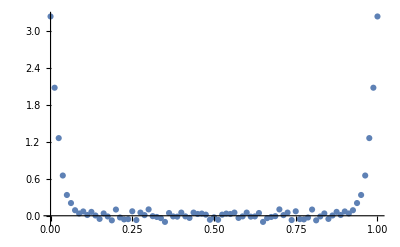

```mathematica
ListPlot[Transpose@{xCoords,fFuncLst},PlotRange->All]
```

```mathematica
fFuncLst=Normal[ExternalEvaluate[sessPy,
"np.load("<>Py[Directory[]<>"\\\\"<>fileName]<>")"]];
```

```mathematica
Dimensions[fFuncLst]
```

{10,4,80,80}

```mathematica
fileName
```

ffunc_distilled_dim_3_N_10_param_divide_[80, 16, 16]_instanceNum_5000_seed_1000.npy

```mathematica
fFuncLst
```

Failure[PythonError,{MessageTemplate:>[Errno 2] No such file or directory: 'D:\\Ohdraw.niL\\Google_drive\\Programming\\Julia\\Modules\\\\ffunc_dim_3_N_40_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_degObj.npy',MessageParameters:><||>,FailureCode:>FileNotFoundError,Traceback:>}]

```mathematica
yy//Length
```

80

```mathematica
gLst
```

PythonError

```mathematica
div
```

80

```mathematica
fileName2
```

ffunc_across_distilled_dim_3_N_10_param_divide_[80, 16, 16]_instanceNum_5000_seed_1000.npy

```mathematica
fileName
```

ffunc_dim_3_N_10_param_divide_[80, 16, 16]_instanceNum_5000_seed_1000.npy

```mathematica
fileNameGlst
```

gDistilled_dim_3_N_10_param_divide_[80, 16, 16]_instanceNum_5000_seed_1000.npy

```mathematica
fFuncScale
```

129.892

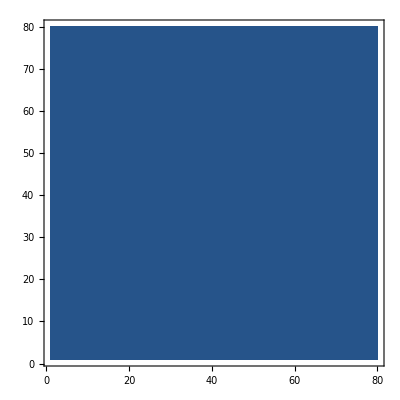

```mathematica
ListContourPlot[fFuncLst⟦1,2⟧]
```

```mathematica
posNegLabel={"\\left< \\lambda_n^+ \\lambda_n^+ \\right>","\\left< \\lambda_n^+ \\lambda_n^- \\right>","\\left<\\lambda_n^+ \\lambda_n^-\\right> - \\left<\\lambda_n^+ \\lambda_n^+\\right>","-+","--"};
```

```mathematica
posNegLabelNbar={"\\left< \\lambda_{\\bar{n}}^+ \\lambda_{\\bar{n}}^+ \\right>","\\left< \\lambda_{\\bar{n}}^+ \\lambda_{\\bar{n}}^- \\right>","\\left<\\lambda_{\\bar{n}}^+ \\lambda_{\\bar{n}}^-\\right> - \\left<\\lambda_{\\bar{n}}^+ \\lambda_{\\bar{n}}^+\\right>","-+","--"};
```

```mathematica
!isAcross
```

False

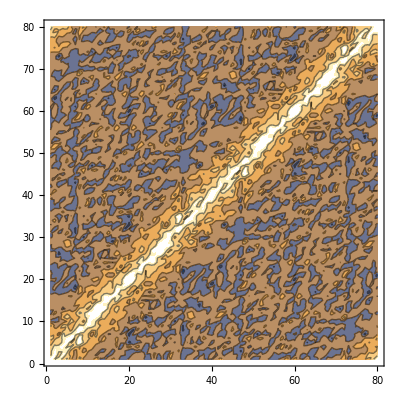

```mathematica
ListContourPlot[fFuncLstBoth⟦1⟧⟦1,2⟧]
```

```mathematica
fileName
```

ffunc_distilled_dim_3_N_10_param_divide_[80, 16, 16]_instanceNum_5000_seed_1000.npy

```mathematica
fileName2
```

ffunc_across_distilled_distilled_dim_3_N_10_param_divide_[80, 16, 16]_instanceNum_5000_seed_1000.npy

```mathematica
fileNameGlst
```

gDistilled_dim_3_N_20_param_divide_[80, 20, 20]_instanceNum_1000_seed_1000.npy

```mathematica
yy
```

{80.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,80.}

```mathematica
fileName2Main<>"_dim_"<>ToString[dim]<>fileNameAttr
```

ffunc_across_distilled_dim_3_N_10_param_divide_[80, 16, 16]_instanceNum_5000_seed_1000

```mathematica
div
```

80

```mathematica
Sum[fFuncLst⟦2,1⟧⟦jj,jj⟧,{jj,1,div}]
```

44.6306

```mathematica
gLst
```

{11.397,20.1218,26.0982,29.5348,30.791,29.591,26.2128,20.267,11.5514}

```mathematica
fileName2<>npyType
```

ffunc_across_distilled_distilled_dim_3_N_10_param_divide_[80, 16, 16]_instanceNum_5000_seed_1000.npy.npy

```mathematica
fileNameMain
```

ffunc_distilled

```mathematica
fileName2Main
```

ffunc_across_distilled

```mathematica
b
```

```mathematica
fileName2Main<>"_dim_"<>ToString[dim]<>fileNameAttr
```

ffunc_across_distilled_dim_3_N_10_param_divide_[80, 16, 16]_instanceNum_5000_seed_1000

```mathematica
coorLstLst=Table[ConstantArray[0,{div+1,Mlst⟦iM⟧,2,polEnd-polStart+1}],{iM,1,Length[Mlst]}];
pltRangeLst=Table[ConstantArray[0,{2,2,Mlst⟦iM⟧,2,polEnd-polStart+1}],{iM,1,Length[Mlst]}];
```

{{0,1},{0.83394,1.33893}}

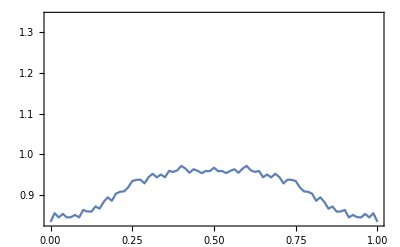

{{0,1},{0.947694,1.33893}}

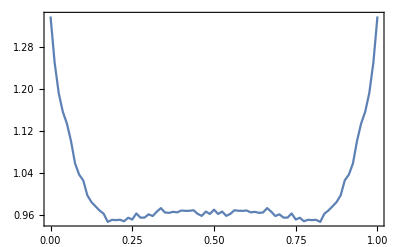

{{0,1},{-0.070044,5.9695}}

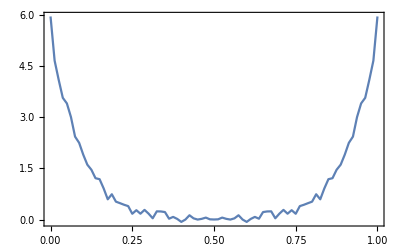

{{0,1},{0.908838,1.25347}}

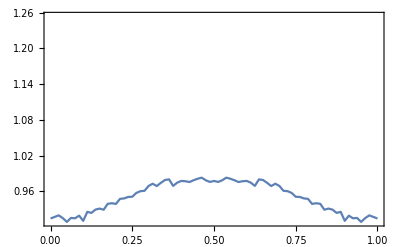

{{0,1},{0.908838,1.25347}}

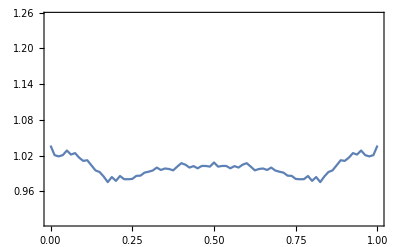

{{0,1},{0.961487,1.25347}}

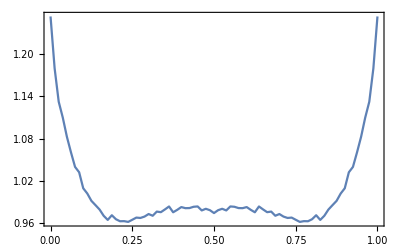

{{0,1},{0.961487,1.25347}}

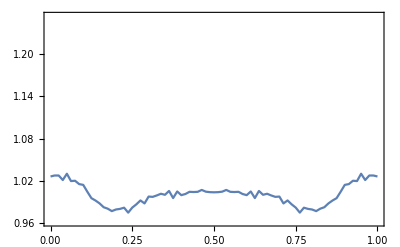

{{0,1},{-0.135769,6.99241}}

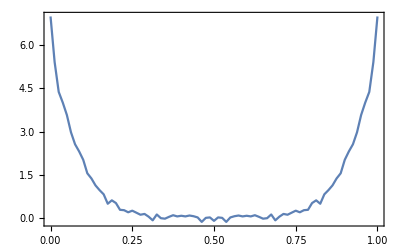

{{0,1},{-0.0108638,1}}

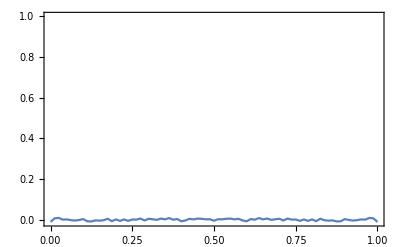

{{0,1},{0.930107,1.21188}}

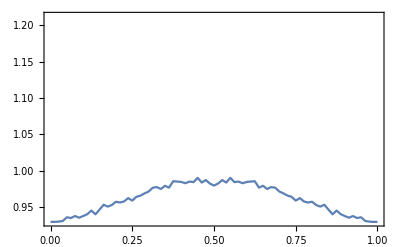

{{0,1},{0.930107,1.21188}}

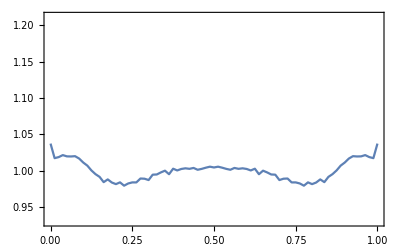

{{0,1},{0.965795,1.21188}}

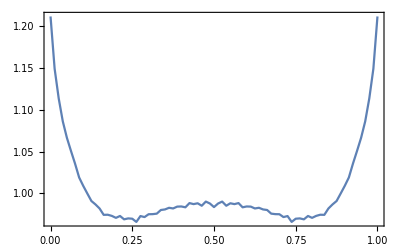

{{0,1},{0.965795,1.21188}}

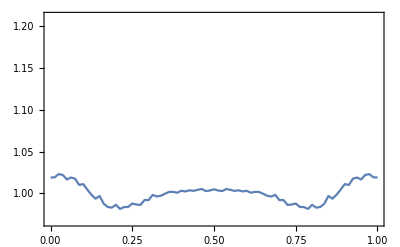

{{0,1},{-0.126993,7.50282}}

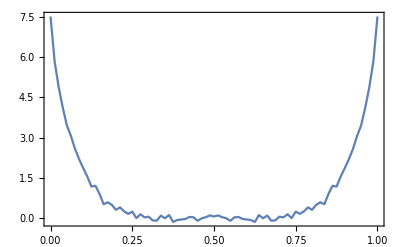

{{0,1},{-0.0186412,1}}

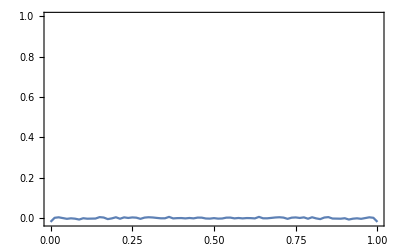

{{0,1},{0.931387,1.19503}}

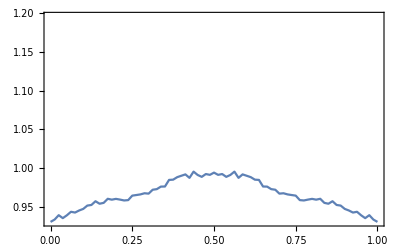

{{0,1},{0.931387,1.19503}}

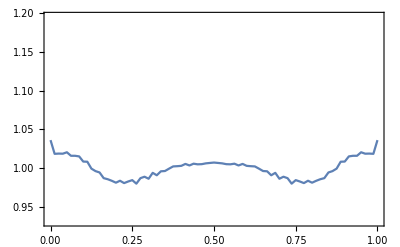

{{0,1},{0.967135,1.19503}}

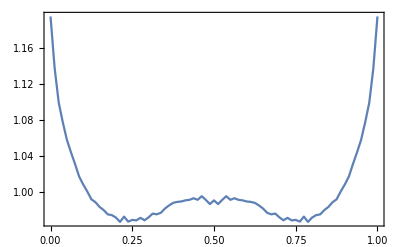

{{0,1},{0.967135,1.19503}}

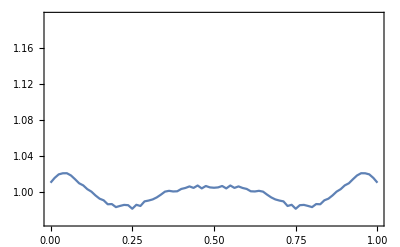

{{0,1},{-0.167533,7.9716}}

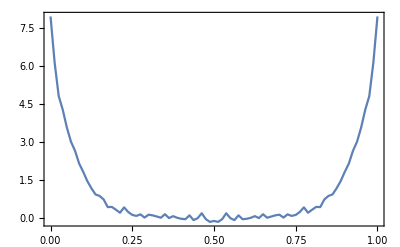

{{0,1},{-0.0258068,1}}

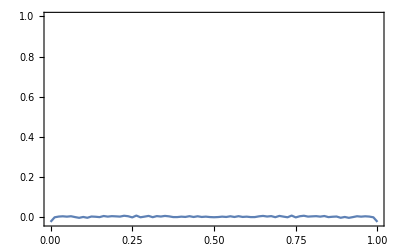

{{0,1},{0.917044,2.87124}}

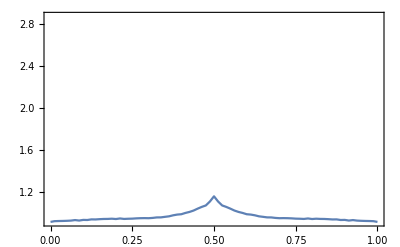

{{0,1},{0.917044,2.87124}}

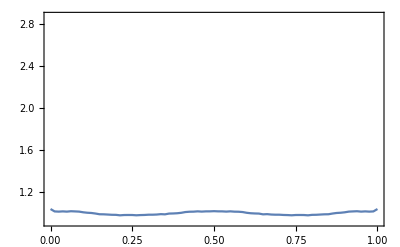

{{0,1},{0.932359,2.87124}}

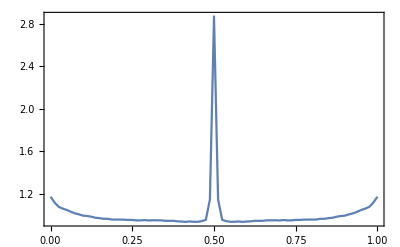

{{0,1},{0.932359,2.87124}}

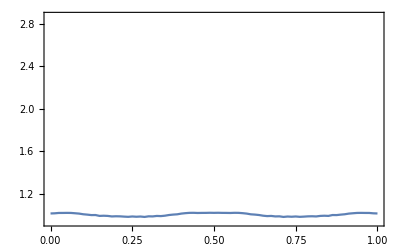

{{0,1},{-3.90947,54.5602}}

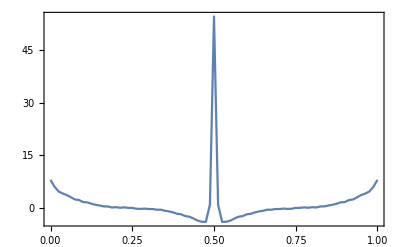

{{0,1},{-0.0275273,1}}

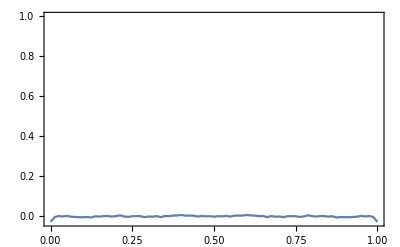

{{0,1},{0.934139,1.1961}}

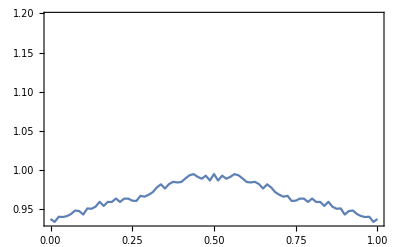

{{0,1},{0.934139,1.1961}}

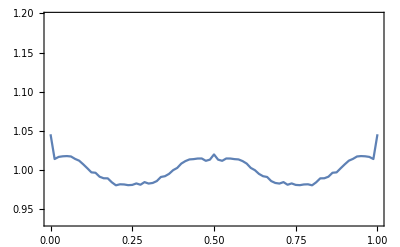

{{0,1},{0.967878,1.1961}}

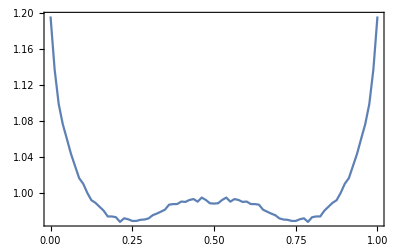

{{0,1},{0.967878,1.1961}}

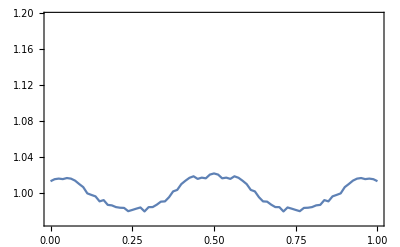

{{0,1},{-0.228789,7.82276}}

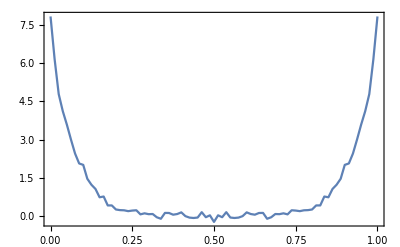

{{0,1},{-0.0329055,1}}

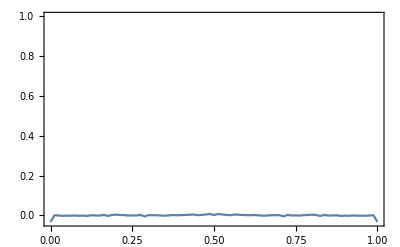

{{0,1},{0.927834,1.21026}}

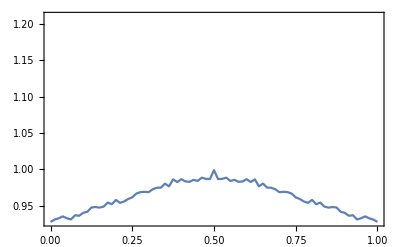

{{0,1},{0.927834,1.21026}}

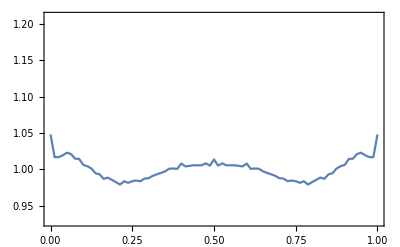

{{0,1},{0.967591,1.21026}}

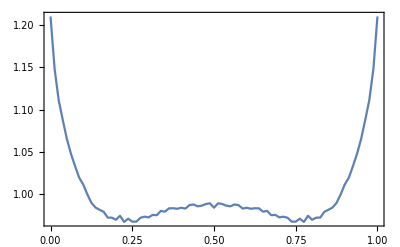

{{0,1},{0.967591,1.21026}}

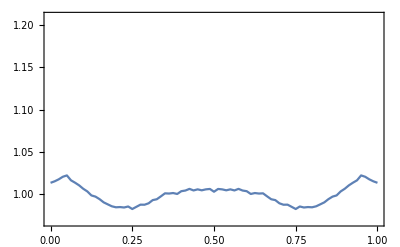

{{0,1},{-0.4121,7.5537}}

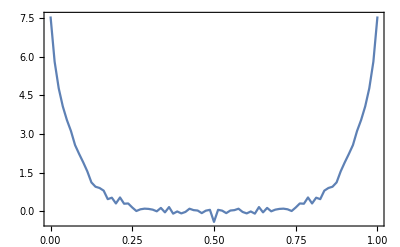

{{0,1},{-0.0343948,1}}

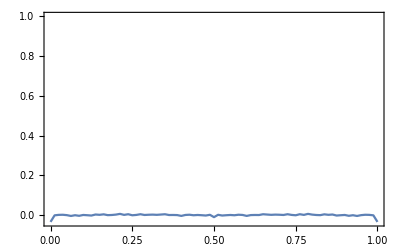

{{0,1},{0.913262,1.25427}}

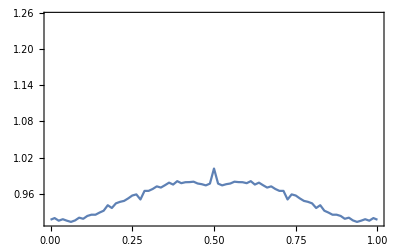

{{0,1},{0.913262,1.25427}}

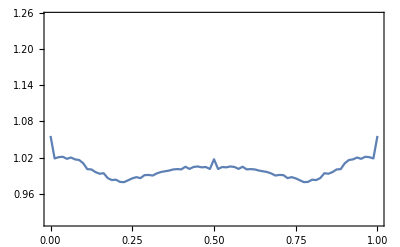

{{0,1},{0.962015,1.25427}}

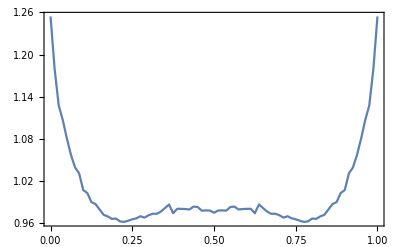

{{0,1},{0.962015,1.25427}}

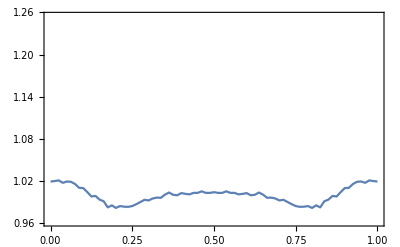

{{0,1},{-0.586427,7.01272}}

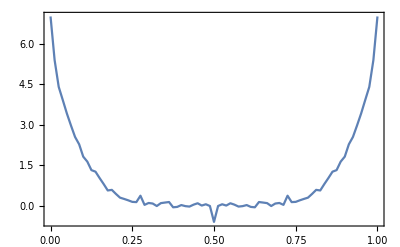

{{0,1},{-0.0366957,1}}

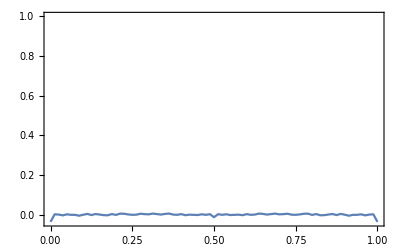

{{0,1},{0.84455,1.33829}}

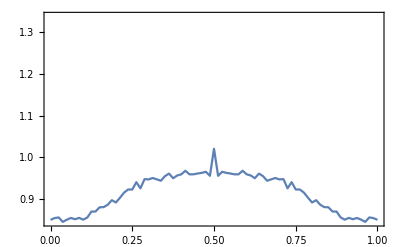

{{0,1},{0.84455,1.33829}}

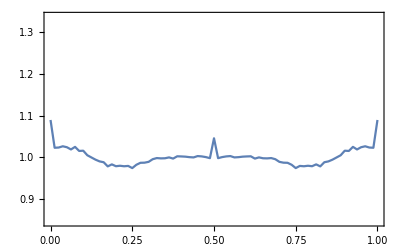

{{0,1},{0.951003,1.33829}}

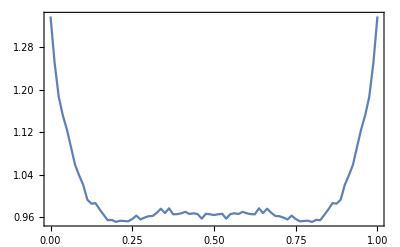

{{0,1},{0.951003,1.33829}}

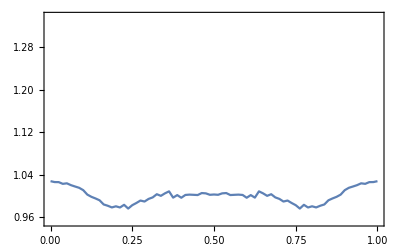

{{0,1},{-0.729073,5.86091}}

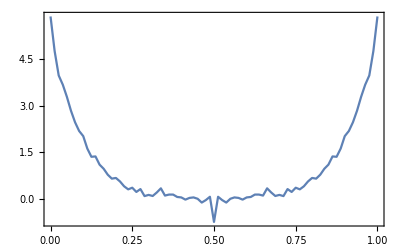

{{0,1},{-0.0619325,1}}

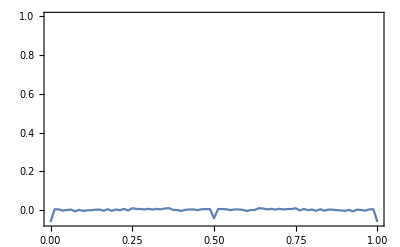

```mathematica
For[itM=1,itM≤Length[Mlst],itM++,
 M=Mlst⟦itM⟧;
fileNameAttrPre="_N_" <>ToString[M];
fileNameAttrFull=fileNameAttrPre;
fileNameAttr=fileNameAttrPre<>"_param_divide_"<>ArrToStrPy[paramDiv]<>"_instanceNum_"<>ToString[instanceNum]<>"_seed_"<>ToString[seed];
fileName=fileNameMain<>"_dim_"<>ToString[dim]<>fileNameAttr;
fileName2=fileName2Main<>"_dim_"<>ToString[dim]<>fileNameAttr;
fileNameGlst=fileGNameMain<>fileNameAttr;
If[fileNameMod≠"",
fileName=nameAppend[fileName,fileNameMod];
fileName2=nameAppend[fileName2,fileNameMod];
fileNameGlst=nameAppend[fileNameGlst,fileNameMod];];
fileName=fileName<>npyType;
fileName2=fileName2<>npyType;
fileNameGlst=fileNameGlst<>npyType;
fFuncLstSame=Normal[ExternalEvaluate[sessPy,
"np.load("<>Py[Directory[]<>"\\\\"<>fileName]<>")"]];
fFuncLstAcross=Normal[ExternalEvaluate[sessPy,
"np.load("<>Py[Directory[]<>"\\\\"<>fileName2]<>")"]];
fFuncLstBoth={fFuncLstSame,fFuncLstAcross};
gLstRaw=Normal[ExternalEvaluate[sessPy,
"np.load("<>Py[Directory[]<>"\\\\"<>fileNameGlst]<>")"]];
gLst=gLstRaw⟦1⟧;
If[isDistilled,Mlim=M-1,Mlim=M];
If[isAcross,Mlim=Mlim-1];
For[m=1,m≤Mlim,m++,
For [idPol=polStart,idPol≤polEnd,idPol++,
For[iAcross=1,iAcross≤2,iAcross++,
If[iAcross==2&&m==1,Break[];];
fFuncLst=fFuncLstBoth⟦iAcross⟧;
mDat=m;
If[iAcross==1,mDat=m,mDat=m-1];
fFuncScale=gLst⟦mDat⟧^2;
dat=fFuncLst⟦mDat,idPol⟧/fFuncScale;
If[idPol==1&&iAcross==1,
dat=(fFuncLst⟦m,idPol⟧-gLst⟦m⟧ /div IdentityMatrix[div])/fFuncScale;
pltRange={{0,1},{Min[fFuncLst⟦m,2⟧/fFuncScale],Max[fFuncLst⟦m,2⟧/fFuncScale]}}];
(*If[idPol==2&&iAcross==1&&(m==M/2||m==M/2+1),
dat=(fFuncLst⟦m,idPol⟧-gLst⟦m⟧ /div RotateLeft[IdentityMatrix[div],div/2])/fFuncScale;
pltRange={{0,1},{Min[fFuncLst⟦m,2⟧/fFuncScale],Max[fFuncLst⟦m,2⟧/fFuncScale]}}];*)
If[idPol==3,
dat=fFuncLst⟦mDat,2⟧-fFuncLst⟦mDat,1⟧;
If[iAcross==1,dat=dat+gLst⟦m⟧ /div IdentityMatrix[div]]];
If[iAcross==2&&idPol==3,dat=dat/gLst⟦mDat⟧/gLst⟦mDat+1⟧,dat=dat/Total[dat,2];];
yy=Wrap0[shAvgWrap[dat]]*div;
If[iAcross==1,pltRange={{0,1},{Min[yy],Max[yy]}};];
If[idPol==1&&iAcross==1,
yy=yy (gLst⟦m⟧^2-gLst⟦m⟧)/gLst⟦m⟧^2;
dat2=fFuncLst⟦m,2⟧/fFuncScale;
dat2=dat2/Total[dat2,2];
yy2=Wrap0[shAvgWrap[dat2]]*div;
pltRange={{0,1},{Min[Min[yy2],Min[yy]],Max[yy2]}};];
coorLstLst⟦itM⟧⟦All,m,iAcross,idPol⟧=yy;
title=MaTeX["M = "<>ToString[M]<>", n = "<>ToString[m]<>", "<>ToString[posNegLabel⟦idPol⟧],Magnification->titleMag];
If[iAcross==2&&idPol==3,pltRange={{0,1},{Min[yy],1}}];
pltRangeLst⟦itM⟧⟦All,All,m,iAcross,idPol⟧=pltRange;
Print[pltRange];
datPlot=ListLinePlot[Transpose@{xCoords,yy},PlotRange->pltRange];
Print[Show[datPlot,BaseStyle->texStyle,PlotLabel->title,FrameLabel->{xyLabs⟦1⟧,Rotate[xyLabs⟦2⟧,-90Degree]},Frame->{{True,False},{True,False}},ImageSize->{Automatic,6cm}]];
]
]
]
]
```

```mathematica
corrTitleLst=MaTeX[#,Magnification->titleMag]&/@posNegLabel
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
corrTitleLstAcross=MaTeX[#,Magnification->titleMag]&/@{"\\left< \\lambda_n^+ \\lambda_{n-1}^+ \\right>","\\left< \\lambda_n^+ \\lambda_{n-1}^- \\right>","\\left< \\lambda_n^+ \\lambda_{n-1}^- \\right> - \\left< \\lambda_n^+ \\lambda_{n-1}^+ \\right>"}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
corrTitleLstNbar=MaTeX[#,Magnification->titleMag]&/@posNegLabelNbar
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
corrTitleLstAcrossNbar=MaTeX[#,Magnification->titleMag]&/@{"\\left< \\lambda_{\\bar{n}}^+ \\lambda_{\\bar{n}-1}^+ \\right>","\\left< \\lambda_{\\bar{n}}^+ \\lambda_{\\bar{n}-1}^- \\right>","\\left< \\lambda_{\\bar{n}}^+ \\lambda_{\\bar{n}-1}^- \\right> - \\left< \\lambda_{\\bar{n}}^+ \\lambda_{\\bar{n}-1}^+ \\right>"}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
corrTitleLstLst={corrTitleLst,corrTitleLstAcross};
```

```mathematica
corrTitleLstLstNbar={corrTitleLstNbar,corrTitleLstAcrossNbar};
```

```mathematica
corrLabK3Lst=MaTeX[#,Magnification->labMagSmall]&/@{"\\left< \\lambda_n^+ \\left( \\chi \\right) \\lambda_n^+ \\left( 0 \\right) \\right>","\\left< \\lambda_n^+ \\left( \\chi \\right) \\lambda_n^- \\left( 0 \\right) \\right>","\\begin{aligned} & \\left< \\lambda_n^+ \\left( \\chi \\right) \\lambda_n^- \\left( 0 \\right) \\right> \\\\ &- \\left< \\lambda_n^+ \\left( \\chi \\right) \\lambda_n^+ \\left( 0 \\right) \\right> \\end{aligned}"}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
corrLabK3LstAcross=MaTeX[#,Magnification->labMagSmall]&/@{"\\left< \\lambda_n^+ \\left( \\chi \\right) \\lambda_{n-1}^+ \\left( 0 \\right) \\right>","\\left< \\lambda_n^+ \\left( \\chi \\right) \\lambda_{n-1}^- \\left( 0 \\right) \\right>","\\begin{aligned} & \\left< \\lambda_n^+ \\left( \\chi \\right) \\lambda_{n-1}^- \\left( 0 \\right) \\right> \\\\ &- \\left< \\lambda_n^+ \\left( \\chi \\right) \\lambda_{n-1}^+ \\left( 0 \\right) \\right> \\end{aligned}"}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
corrLabK3LstNbar=MaTeX[#,Magnification->labMagSmall]&/@{"\\left< \\lambda_{\\bar{n}}^+ \\left( 0 \\right) \\lambda_{\\bar{n}}^+ \\left( k_3 \\right) \\right>","\\left< \\lambda_{\\bar{n}}^+ \\left( 0 \\right) \\lambda_{\\bar{n}}^- \\left( k_3 \\right) \\right>","\\begin{aligned} & \\left< \\lambda_{\\bar{n}}^+ \\left( 0 \\right) \\lambda_{\\bar{n}}^- \\left( k_3 \\right) \\right> \\\\ &- \\left< \\lambda_{\\bar{n}}^+ \\left( 0 \\right) \\lambda_{\\bar{n}}^+ \\left( k_3 \\right) \\right> \\end{aligned}"}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
corrLabK3LstAcrossNbar=MaTeX[#,Magnification->labMagSmall]&/@{"\\left< \\lambda_{\\bar{n}}^+ \\left( 0 \\right) \\lambda_{\\bar{n}-1}^+ \\left( k_3 \\right) \\right>","\\left< \\lambda_{\\bar{n}}^+ \\left( 0 \\right) \\lambda_{\\bar{n}-1}^- \\left( k_3 \\right) \\right>","\\begin{aligned} & \\left< \\lambda_{\\bar{n}}^+ \\left( 0 \\right) \\lambda_{\\bar{n}-1}^- \\left( k_3 \\right) \\right> \\\\ &- \\left< \\lambda_{\\bar{n}}^+ \\left( 0 \\right) \\lambda_{\\bar{n}-1}^+ \\left( k_3 \\right) \\right> \\end{aligned}"}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
corrLabK3LstLst={corrLabK3Lst,corrLabK3LstAcross};
```

```mathematica
corrLabK3LstLstNbar={corrLabK3LstNbar,corrLabK3LstAcrossNbar};
```

```mathematica
funPlotLst=ConstantArray[0,{2,3}];
```

```mathematica
funPlotLst
```

{{0,0,0},{0,0,0}}

```mathematica
labFuncLst={{capTex⟦2⟧,capTex⟦1⟧,capTex⟦3⟧},capTex};
```

```mathematica
pltRangeLst⟦1⟧⟦2,2,m,1,1⟧=1.2
```

1.2

```mathematica
pltRangeLst⟦1⟧⟦All,All,m,2,All⟧
```

{{{0,0,0},{1,1,1}},{{0.917044,0.932359,-0.0275273},{2.87124,2.87124,1}}}

```mathematica
M
```

10

```mathematica
datTest=coorLstLst⟦1⟧⟦All,m,1,2⟧
```

{1.17039,1.11494,1.07434,1.05743,1.04477,1.02719,1.01283,1.00295,0.99094,0.987995,0.981245,0.971369,0.967768,0.961702,0.961543,0.954511,0.954261,0.95431,0.953435,0.950612,0.951165,0.946596,0.946527,0.949929,0.945789,0.948111,0.946938,0.94733,0.94285,0.942049,0.943022,0.937678,0.935913,0.932359,0.936476,0.933528,0.933325,0.939455,0.952155,1.14386,2.87124,1.14386,0.952155,0.939455,0.933325,0.933528,0.936476,0.932359,0.935913,0.937678,0.943022,0.942049,0.94285,0.94733,0.946938,0.948111,0.945789,0.949929,0.946527,0.946596,0.951165,0.950612,0.953435,0.95431,0.954261,0.954511,0.961543,0.961702,0.967768,0.971369,0.981245,0.987995,0.99094,1.00295,1.01283,1.02719,1.04477,1.05743,1.07434,1.11494,1.17039}

```mathematica
datTestCrop=datTest;
```

```mathematica
datTestCrop⟦38⟧=datTestCrop⟦39⟧=datTestCrop⟦40⟧=datTestCrop⟦41⟧=datTestCrop⟦42⟧=datTestCrop⟦43⟧=datTestCrop⟦44⟧=datTestCrop⟦45⟧
```

0.933325

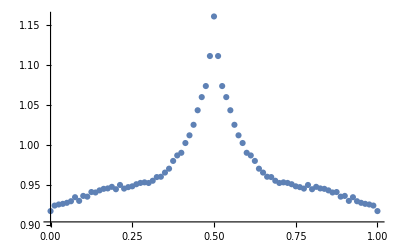

```mathematica
ListPlot[{xCoords,coorLstLst⟦1⟧⟦All,m,1,1⟧}ᵀ]
```

```mathematica
iAcross=1;coorId=2;
```

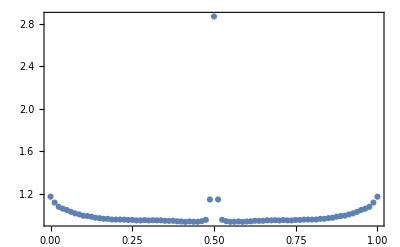

```mathematica
Show[ListPlot[{xCoords,coorLstLst⟦1⟧⟦All,m,1,2⟧}ᵀ,PlotRange->pltRangeLst⟦1⟧⟦All,All,m,iAcross,coorId⟧],BaseStyle->texStyle,PlotLabel->corrTitleLstLstNbar⟦iAcross⟧⟦coorId⟧,FrameLabel->{xyLabs⟦1⟧,Rotate[corrLabK3LstLstNbar⟦iAcross⟧⟦coorId⟧,0Degree]},Frame->True,ImageSize->{Automatic,9cm}]
```

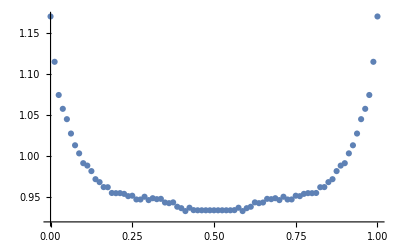

```mathematica
ListPlot[{xCoords,datTestCrop}ᵀ]
```

```mathematica
pltRangeLst⟦1⟧⟦All,All,4,All,All⟧
```

{{{{0,0,0},{0,0,0}},{{1,1,1},{1,1,1}}},{{{0.931387,0.967135,-0.167533},{0.931387,0.967135,-0.0258068}},{{1.19503,1.19503,7.9716},{1.19503,1.19503,1}}}}

```mathematica
pltRangeLst⟦1⟧⟦All,All,4,1,3⟧
```

{{0,1},{-0.167533,7.9716}}

```mathematica
pltRangeLst4={{{{0,1},{0.90,1.20}},{{0,1},{0.90,1.20}},{{0,1},{-0.2,8}}},{{{0,1},{0.90,1.20}},{{0,1},{0.90,1.20}},{{0,1},{-0.05,0.05}}}};
```

```mathematica
dataThick
```

AbsoluteThickness[1]

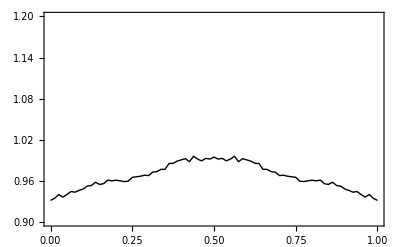

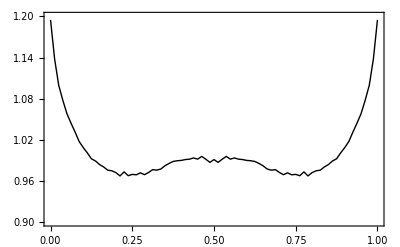

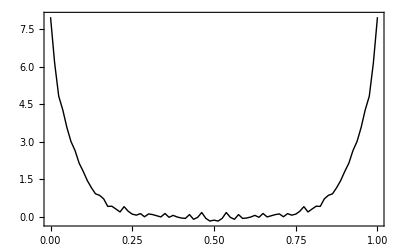

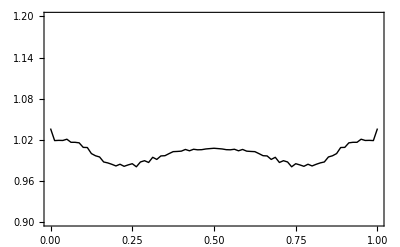

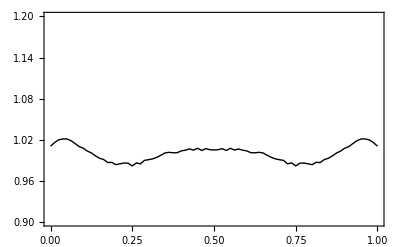

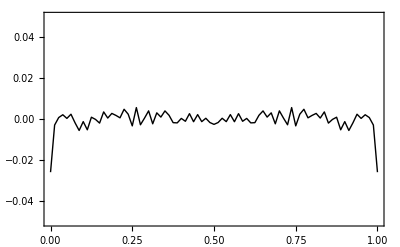

```mathematica
coorId=2;
m=4;
For[iAcross=1,iAcross≤2,iAcross++,
For[coorId=1,coorId≤3,coorId++,
datPlot=ListLinePlot[Transpose@{xCoords,coorLstLst⟦1⟧⟦All,m,iAcross,coorId⟧},PlotStyle->{Black,dataThick}(*,PlotRange->pltRangeLst⟦1⟧⟦All,All,m,iAcross,coorId⟧*),PlotRange->pltRangeLst4⟦iAcross,coorId,All,All⟧];
(*If [m==M/2 && coorId==1 && iAcross==1,datArr=coorLstLst⟦1⟧⟦All,m,iAcross,coorId⟧,];*)
funPlotLst⟦iAcross,coorId⟧=Show[datPlot,Graphics[Text[labFuncLst⟦iAcross,coorId⟧,Scaled[{0.1,0.85}]]],BaseStyle->texStyle,(*PlotLabel->corrTitleLstLst⟦iAcross⟧⟦coorId⟧,*)FrameLabel->{xyLabs⟦1⟧,Rotate[corrLabK3LstLst⟦iAcross⟧⟦coorId⟧,0Degree]},Frame->True,ImageSize->{Automatic,5cm}];
Print[funPlotLst⟦iAcross,coorId⟧];
]]
```

```mathematica
m=4
```

4

```mathematica
corrTitleLst⟦2⟧
```

-Graphics-

```mathematica
legPm=MaTeX[#,Magnification->labMagSmall]&/@{"\\langle \\lambda_n^+ \\lambda_n^- \\rangle","\\langle \\lambda_n^+ \\lambda_n^+ \\rangle"};
```

```mathematica
legPm
```

{-Graphics-,-Graphics-}

```mathematica
datPlot=ListLinePlot[{Transpose@{xCoords,coorLstLst⟦1⟧⟦All,m,2,2⟧},Transpose@{xCoords,coorLstLst⟦1⟧⟦All,m,2,1⟧}}(*,PlotRange->pltRangeLst⟦1⟧⟦All,All,m,iAcross,coorId⟧*),PlotRange->{{0,1},{0.90,1.20}},PlotStyle->{{Black,dataThick},{ColorData[112,1],Dashed,1.5dataThick}},PlotLegends->Placed[LineLegend[legPm,LegendMarkerSize->18,Spacings->0.05],{{0.6,0.7},Right}]];
```

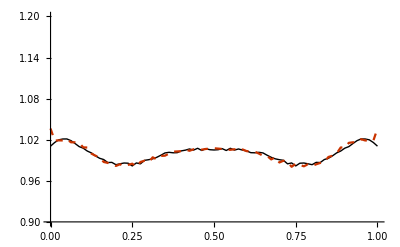

```mathematica
datPlot
```

```mathematica
coorLabPm=MaTeX[#,Magnification->labMag]&/@{"\\langle \\lambda_n^+ \\rangle \\left( \\chi \\right) \\lambda_{n-1}^{\\pm} \\left( 0 \\right)"}
```

{-Graphics-}

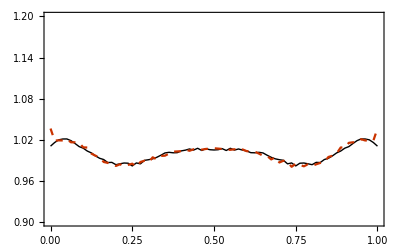

```mathematica
Show[datPlot,Graphics[Text[capTex⟦1⟧,Scaled[{0.1,0.85}]]],BaseStyle->texStyle,(*PlotLabel->corrTitleLstLst⟦iAcross⟧⟦coorId⟧,*)FrameLabel->{xyLabs⟦1⟧,Rotate[coorLabPm⟦1⟧,0Degree]},Frame->True,ImageSize->{Automatic,5cm}]
```

```mathematica
datPlotDiff=ListLinePlot[Transpose@{xCoords,coorLstLst⟦1⟧⟦All,m,2,3⟧}(*,PlotRange->pltRangeLst⟦1⟧⟦All,All,m,iAcross,coorId⟧*),PlotRange->{{0,1},{-0.05,0.05}},PlotStyle->{Black,dataThick}];
```

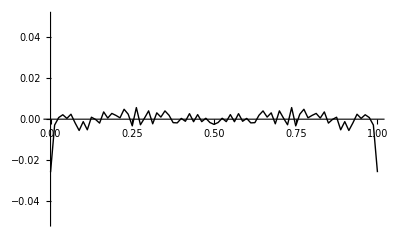

```mathematica
datPlotDiff
```

```mathematica
Show[datPlotDiff,Graphics[Text[capTex⟦2⟧,Scaled[{0.1,0.85}]]],BaseStyle->texStyle,(*PlotLabel->corrTitleLstLst⟦iAcross⟧⟦coorId⟧,*)FrameLabel->{xyLabs⟦1⟧,Rotate[corrLabK3LstLst⟦2⟧⟦3⟧,0Degree]},Frame->True,ImageSize->{Automatic,5cm}]
```

-Graphics-

```mathematica
iAcross=1;coorId=2;
```

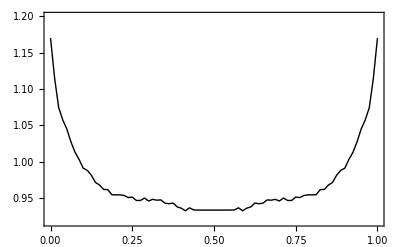

```mathematica
datPlot=ListLinePlot[Transpose@{xCoords,datTestCrop},PlotStyle->{Black,dataThick},PlotRange->pltRangeLst⟦1⟧⟦All,All,m,iAcross,1⟧];
Show[datPlot,Graphics[Text[labFuncLst⟦iAcross,3⟧,Scaled[{0.1,0.85}]]],BaseStyle->texStyle,PlotLabel->corrTitleLstLstNbar⟦iAcross⟧⟦coorId⟧,FrameLabel->{xyLabs⟦1⟧,Rotate[corrLabK3LstLstNbar⟦iAcross⟧⟦coorId⟧,0Degree]},Frame->True,ImageSize->{Automatic,5cm}]
```

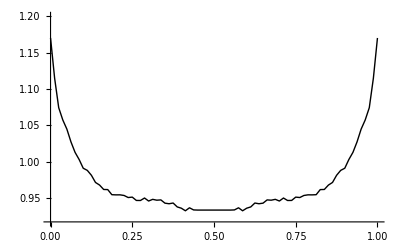

```mathematica
Show[datPlot,ImageSize->{Automatic,5cm}]
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Part::partw: Part 3 of … does not exist.

Show::gcomb: Could not combine the graphics objects in Show[{{{,,},{,,}}⟦3,4⟧,}].

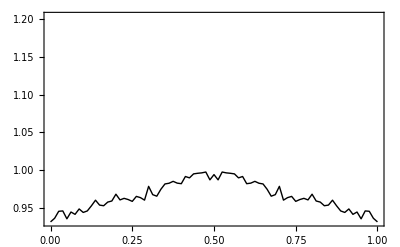
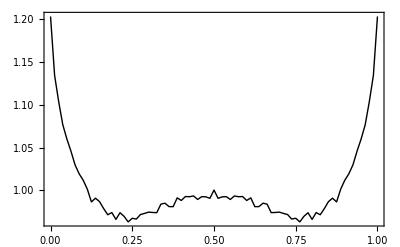
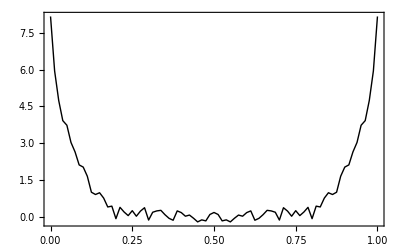
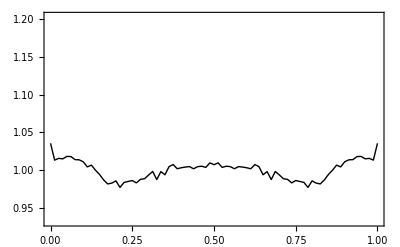
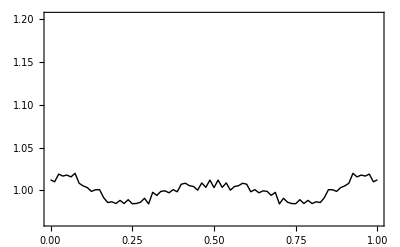
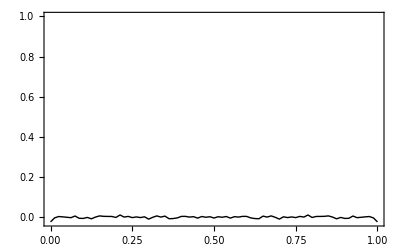
Show[{{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}⟦3,4⟧,-Graphics-}]

```mathematica
Show[{funPlotLst⟦iAcross,coorId⟧,Graphics[Text[capTex⟦1⟧,Scaled[{0.1,0.9}]]]}]
```

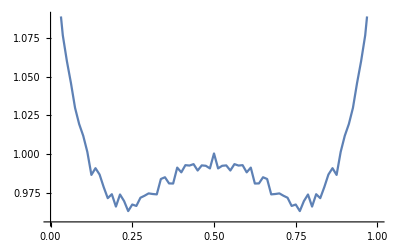

```mathematica
ListLinePlot[Transpose@{xCoords,coorLstLst⟦1⟧⟦All,4,1,2⟧}]
```

```mathematica
m=4;div=80;
```

```mathematica
dat=fFuncLst⟦m,2⟧-(fFuncLst⟦m,1⟧-gLst⟦m⟧ /div IdentityMatrix[div]);
```

```mathematica
idPol=3;
```

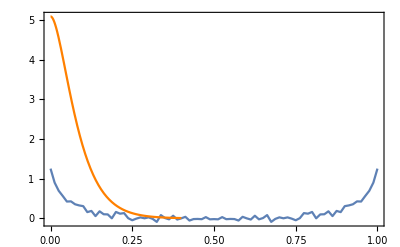

```mathematica
yy=Wrap0[shAvgWrap[dat]]*div;
yy=(div/(2π))yy/Total[yy] ;
title=MaTeX["M = "<>ToString[M]<>", n = "<>ToString[m]<>", "<>ToString[posNegLabel⟦idPol⟧],Magnification->1.4];
datPlot=ListLinePlot[Transpose@{xCoords,yy},PlotRange->All];
Print[Show[datPlot,Plot[expXFit[x],{x,0,0.4},PlotStyle->Orange,PlotRange->All],BaseStyle->texStyle,PlotLabel->title,PlotRange-> All,FrameLabel->xyLabs,Frame->{{True,False},{True,False}}]];
```

```mathematica
dataFit={xCoords,yy}ᵀ;
```

```mathematica
ListPlot[dataFit]
```

```mathematica
dataFit//Dimensions
```

{81,2}

```mathematica
xCoords⟦1⟧
```

0

```mathematica
powerFit=NonlinearModelFit[dataFit⟦2;;15,All⟧,a x^-b,{a,b},x];
```

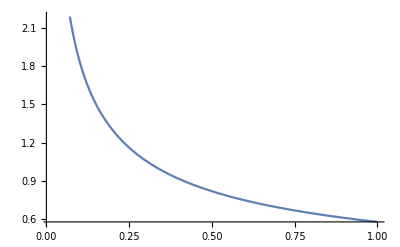

```mathematica
Plot[powerFit[x],{x,1/80,1}]
```

```mathematica
expFit=NonlinearModelFit[dataFit⟦1;;10,All⟧,a Exp[-b x],{a,b},x];
```

```mathematica
expXFit=NonlinearModelFit[dataFit⟦1;;15,All⟧,a (b+x) Exp[-x/b],{a,b},x];
```

```mathematica
GaussianFit=NonlinearModelFit[dataFit⟦1;;10,All⟧,a Exp[-b x^2],{a,b},x];
```

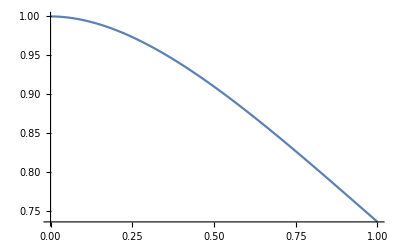

```mathematica
Plot[(x+1)Exp[-x],{x,0,1}]
```

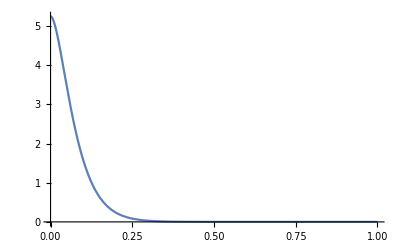

```mathematica
Plot[expXFit[x],{x,0,1},PlotRange->All]
```

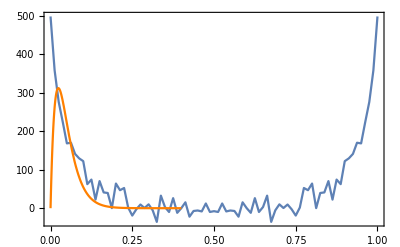

```mathematica
yy=Wrap0[shAvgWrap[dat]]*div;
title=MaTeX["M = "<>ToString[M]<>", n = "<>ToString[m]<>", "<>ToString[posNegLabel⟦idPol⟧],Magnification->1.4];
datPlot=ListLinePlot[Transpose@{xCoords,yy},PlotRange->All];
Print[Show[datPlot,Plot[expXFit[x],{x,0,0.4},PlotStyle->Orange,PlotRange->All],BaseStyle->texStyle,PlotLabel->title,PlotRange-> All,FrameLabel->xyLabs,Frame->{{True,False},{True,False}}]];
```

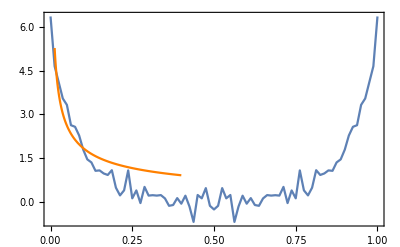

```mathematica
yy=Wrap0[shAvgWrap[dat]]*div;
title=MaTeX["M = "<>ToString[M]<>", n = "<>ToString[m]<>", "<>ToString[posNegLabel⟦idPol⟧],Magnification->1.4];
datPlot=ListLinePlot[Transpose@{xCoords,yy},PlotRange->All];
Print[Show[datPlot,Plot[powerFit[x],{x,1/80,0.4},PlotStyle->Orange,PlotRange->All],BaseStyle->texStyle,PlotLabel->title,PlotRange-> All,FrameLabel->xyLabs,Frame->{{True,False},{True,False}}]];
```

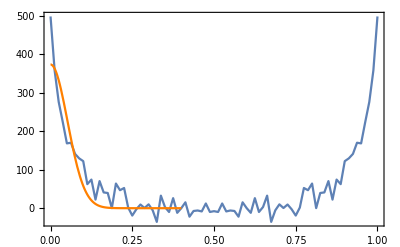

```mathematica
yy=Wrap0[shAvgWrap[dat]]*div;
title=MaTeX["M = "<>ToString[M]<>", n = "<>ToString[m]<>", "<>ToString[posNegLabel⟦idPol⟧],Magnification->1.4];
datPlot=ListLinePlot[Transpose@{xCoords,yy},PlotRange->All];
Print[Show[datPlot,Plot[GaussianFit[x],{x,0,0.4},PlotStyle->Orange,PlotRange->All],BaseStyle->texStyle,PlotLabel->title,PlotRange-> All,FrameLabel->xyLabs,Frame->{{True,False},{True,False}}]];
```

```mathematica
fFuncLst⟦4,1⟧-gLst⟦4⟧ IdentityMatrix
```

{{1.221-56.982 IdentityMatrix,0.502-56.982 IdentityMatrix,0.50575-56.982 IdentityMatrix,0.52025-56.982 IdentityMatrix,73,0.5325-56.982 IdentityMatrix,0.531-56.982 IdentityMatrix,0.521-56.982 IdentityMatrix},78,{1}}
 |  |  |  |

```mathematica
Total[yy⟦1;;-2⟧]
```

80.1053

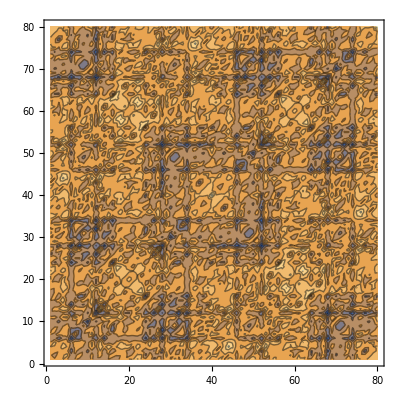

```mathematica
ListContourPlot[fFuncLst⟦4,1⟧-gLst⟦4⟧/80 IdentityMatrix[80]]
```

```mathematica
fFuncLst⟦4,1,1,1⟧
```

1.221

```mathematica
gLst⟦4⟧/80
```

0.712275

```mathematica
Total[dat,2]
```

1.

```mathematica
yy
```

{0.,0.239,0.469,0.651,0.834,0.951,1.086,1.18,1.293,1.41,1.511,1.559,1.654,1.68,1.74,1.71,1.699,1.674,1.674,1.735,1.737,1.731,1.713,1.726,1.698,1.725,1.711,1.763,1.784,1.779,1.787,1.815,1.83,1.838,1.885,1.882,1.939,1.864,1.889,1.891,1.88,1.848,1.867,1.794,1.769,1.734,1.739,1.801,1.769,1.828,1.847,1.874,1.837,1.94,1.961,1.907,1.852,1.872,1.876,1.923,1.891,1.866,1.789,1.768,1.692,1.677,1.707,1.627,1.604,1.535,1.484,1.486,1.39,1.304,1.153,0.955,0.853,0.707,0.492,0.246,0.}

```mathematica
gLst
```

{{11.543,32.221,47.344,56.883,61.424,61.424,56.883,47.344,32.221,11.543},{11.543,32.22,47.344,56.882,61.424,61.424,56.882,47.344,32.22,11.543}}

```mathematica
2gLst⟦1⟧xCoords(1-xCoords)
```

{0.,0.284968,0.562721,0.83326,1.09659,1.3527,1.60159,1.84327,2.07774,2.30499,2.52503,2.73786,2.94346,3.14186,3.33304,3.51701,3.69376,3.8633,4.02562,4.18073,4.32863,4.46931,4.60277,4.72902,4.84806,4.95988,5.06449,5.16189,5.25207,5.33503,5.41078,5.47932,5.54064,5.59475,5.64164,5.68132,5.71379,5.73904,5.75707,5.76789,5.7715,5.76789,5.75707,5.73904,5.71379,5.68132,5.64164,5.59475,5.54064,5.47932,5.41078,5.33503,5.25206,5.16189,5.06449,4.95988,4.84806,4.72902,4.60277,4.46931,4.32863,4.18073,4.02562,3.8633,3.69376,3.51701,3.33304,3.14186,2.94346,2.73786,2.52503,2.30499,2.07774,1.84327,1.60159,1.3527,1.09659,0.83326,0.562721,0.284968,0.}

```mathematica
?MaTeX
```

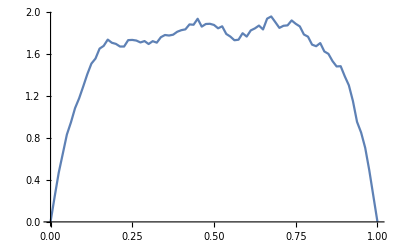

```mathematica
datPlot
```

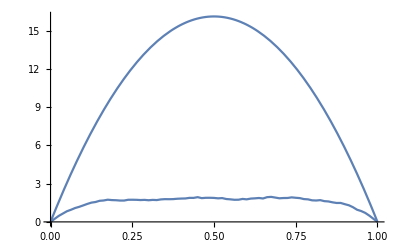

```mathematica
Show[uncorrPlot,datPlot]
```

```mathematica
ListLinePlot[Transpose@{xCoords,yy}]
```

-Graphics-

```mathematica
nameAppend[fileName,fileNameMod]
```

deltaN_N_10_param_divide_[80 16 16]_instanceNum_1000_seed_1000_threadedMKLtest.npy_threadedMKLtest

```mathematica
fileName
```

deltaN_N_10_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_threadedMKLTest.npy

```mathematica
""==""
```

True

```mathematica
ArrToStrPy[paramDiv]
```

[, 80, 16, 16]

```mathematica
Py[fileName]
```

"deltaN_N_10_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_threadedMKLTest.npy"

```mathematica
ExternalEvaluate["Python",
"import os
print(os.getcwd())"]
```

D:\Ohdraw.niL\Google_drive\Programming\Julia\Modules

```mathematica
fileNameTest="deltaN_N_10_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_threadedMKLTest.npy";
```

```mathematica
Py[fileNameTest]
```

"deltaN_N_10_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_threadedMKLTest.npy"

```mathematica
Py[Directory[]]
```

"D:\\Ohdraw.niL\\Google_drive\\Programming\\Julia\\Modules"

```mathematica
Py[Directory[]]<>Py[fileNameTest]
```

"D:\\Ohdraw.niL\\Google_drive\\Programming\\Julia\\Modules""deltaN_N_10_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_threadedMKLTest.npy"

```mathematica
"\\\\"
```

\\

```mathematica
Py[Directory[]<>"\\\\"<>fileNameTest]
```

"D:\\Ohdraw.niL\\Google_drive\\Programming\\Julia\\Modules\\\\deltaN_N_10_param_divide_[80, 16, 16]_instanceNum_1000_seed_1000_threadedMKLTest.npy"

```mathematica
deltaNLst=Normal[ExternalEvaluate[sessPy,
"import numpy as np
np.load("<>Py[Directory[]<>"\\\\"<>fileNameTest]<>")"]];
```

```mathematica
deltaNLst⟦10,-1⟧
```

0.

```mathematica
{deltaNLst⟦1,-1⟧}~Join~deltaNLst⟦1⟧
```

{0.,0.242,0.471,0.672,0.859,1.004,1.139,1.233,1.271,1.374,1.483,1.592,1.599,1.664,1.671,1.613,1.63,1.7,1.748,1.841,1.791,1.862,1.797,1.854,1.852,1.839,1.847,1.843,1.884,1.849,1.822,1.92,1.92,1.882,1.885,1.795,1.795,1.839,1.844,1.83,1.88,1.889,1.843,1.921,1.892,1.903,1.838,1.858,1.845,1.84,1.933,1.863,1.958,1.902,1.922,1.918,1.911,1.85,1.85,1.883,1.843,1.815,1.785,1.8,1.71,1.673,1.649,1.603,1.588,1.551,1.505,1.381,1.288,1.224,1.111,0.994,0.851,0.676,0.523,0.295,0.}

```mathematica
xCoords=1/div Table[x,{x,0,div}];
```

```mathematica
xCoords
```

{0,1/80,1/40,3/80,1/20,1/16,3/40,7/80,1/10,9/80,1/8,11/80,3/20,13/80,7/40,3/16,1/5,17/80,9/40,19/80,1/4,21/80,11/40,23/80,3/10,5/16,13/40,27/80,7/20,29/80,3/8,31/80,2/5,33/80,17/40,7/16,9/20,37/80,19/40,39/80,1/2,41/80,21/40,43/80,11/20,9/16,23/40,47/80,3/5,49/80,5/8,51/80,13/20,53/80,27/40,11/16,7/10,57/80,29/40,59/80,3/4,61/80,31/40,63/80,4/5,13/16,33/40,67/80,17/20,69/80,7/8,71/80,9/10,73/80,37/40,15/16,19/20,77/80,39/40,79/80,1}

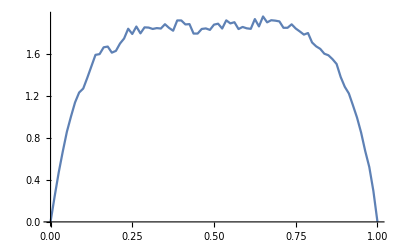

```mathematica
fig=ListLinePlot[Transpose@{xCoords,{deltaNLst⟦1,-1⟧}~Join~deltaNLst⟦1⟧}]
```

```mathematica
Head[fig]
```

Graphics

```mathematica
Normal[deltaNLst]
```

{{0.242,0.471,0.672,0.859,1.004,1.139,1.233,1.271,1.374,1.483,1.592,1.599,1.664,1.671,1.613,1.63,1.7,1.748,1.841,1.791,1.862,1.797,1.854,1.852,1.839,1.847,1.843,1.884,1.849,1.822,1.92,1.92,1.882,1.885,1.795,1.795,1.839,1.844,1.83,1.88,1.889,1.843,1.921,1.892,1.903,1.838,1.858,1.845,1.84,1.933,1.863,1.958,1.902,1.922,1.918,1.911,1.85,1.85,1.883,1.843,1.815,1.785,1.8,1.71,1.673,1.649,1.603,1.588,1.551,1.505,1.381,1.288,1.224,1.111,0.994,0.851,0.676,0.523,0.295,0.},{0.71,1.355,1.839,2.34,2.783,3.099,3.249,3.341,3.522,3.669,3.838,3.951,4.004,4.135,4.161,4.236,4.444,4.315,4.512,4.396,4.486,4.454,4.799,4.833,4.692,4.62,4.689,4.781,4.615,4.58,4.603,4.545,4.427,4.319,4.159,4.382,4.522,4.408,4.39,4.52,4.486,4.455,4.537,4.637,4.488,4.48,4.652,4.576,4.502,4.562,4.392,4.383,4.476,4.486,4.389,4.347,4.528,4.393,4.51,4.473,4.527,4.517,4.458,4.367,4.302,4.335,4.194,4.241,4.096,3.933,3.803,3.49,3.216,2.841,2.515,2.25,1.911,1.346,0.756,0.001},{1.071,2.011,2.58,3.22,3.637,4.234,4.528,4.61,4.969,5.107,5.12,5.171,5.191,5.556,5.669,5.758,5.899,5.779,5.685,5.928,6.025,5.974,5.922,5.772,5.858,5.62,5.752,5.885,5.802,5.704,5.742,5.902,5.779,5.671,5.704,5.835,5.83,5.595,5.638,5.673,5.769,5.585,5.566,5.891,5.74,5.67,5.464,5.314,5.547,5.601,5.914,5.992,5.752,5.966,6.214,6.303,6.236,6.034,6.369,6.169,6.199,6.054,5.902,5.846,5.488,5.647,5.48,5.262,5.225,5.184,5.064,4.894,4.565,4.36,3.846,3.287,2.69,1.835,1.032,0.},{1.113,2.205,2.971,3.822,4.523,5.061,5.538,5.628,5.738,5.766,6.096,6.252,6.207,6.144,6.365,6.44,6.526,6.404,6.531,6.625,6.593,6.797,6.894,6.577,6.674,6.599,6.458,6.413,6.491,6.604,6.701,6.641,6.453,6.651,6.762,6.506,6.683,6.769,6.542,6.295,6.315,6.223,6.389,6.701,6.935,6.685,6.655,6.555,6.634,6.527,6.735,6.837,6.859,6.892,7.071,6.943,6.851,6.883,6.701,6.743,6.737,6.918,7.071,6.941,6.856,6.54,6.504,6.699,6.477,6.268,6.126,5.956,5.406,5.219,4.643,3.906,3.148,2.484,1.301,0.001},{1.32,2.322,3.253,3.973,4.658,5.253,5.623,5.779,5.742,6.359,6.767,7.063,7.159,6.991,7.349,7.394,7.314,7.11,7.143,7.219,7.185,7.453,7.639,7.249,7.323,6.768,6.879,6.817,6.859,6.751,6.783,6.741,6.938,7.078,7.753,8.303,8.566,9.256,9.865,10.513,10.278,9.674,9.117,8.67,8.52,8.338,7.957,7.942,7.793,7.829,7.387,7.451,7.402,7.364,7.485,7.4,7.393,7.321,7.198,7.213,6.942,6.859,7.185,7.109,6.95,6.944,7.14,7.432,7.241,6.957,6.622,6.58,5.865,5.476,4.912,4.185,3.616,2.658,1.374,0.},{1.217,2.367,3.336,4.245,5.023,5.543,5.774,5.797,6.366,6.404,6.59,6.748,6.807,6.935,7.324,7.221,7.13,6.816,7.019,7.04,7.001,6.976,7.438,7.192,7.273,6.763,7.199,7.285,7.288,7.072,7.229,7.375,7.438,7.769,7.985,8.324,8.587,9.025,9.559,10.513,9.979,9.815,9.342,8.73,8.413,8.144,7.876,7.64,7.441,7.16,6.908,7.242,7.32,7.244,7.216,7.183,6.805,7.001,6.904,6.922,6.742,6.752,6.978,6.962,6.844,6.891,6.912,6.93,6.792,6.596,6.504,6.112,5.805,5.287,5.21,4.364,3.507,2.565,1.342,0.},{1.328,2.414,3.21,4.064,4.834,5.072,5.21,5.588,5.911,5.836,5.864,6.112,6.07,6.191,6.358,6.472,6.774,6.84,6.688,6.768,7.012,7.273,7.074,6.996,6.881,6.539,6.675,6.724,6.63,6.549,6.181,6.213,6.127,6.412,6.43,6.425,6.479,6.433,6.152,6.298,6.503,6.673,6.857,6.766,6.789,6.851,6.996,6.744,6.28,6.192,6.458,6.78,6.663,6.532,6.711,6.49,6.406,6.366,6.539,6.601,6.629,6.539,6.544,6.249,6.218,6.079,6.028,5.859,5.749,5.93,5.565,5.465,4.959,5.033,4.752,3.882,3.145,2.305,1.31,0.001},{1.018,1.898,2.521,3.342,3.819,4.265,4.397,4.799,5.244,5.468,5.693,5.711,5.561,5.749,6.099,6.104,6.119,6.037,6.222,6.138,6.286,6.155,5.807,5.981,5.797,5.776,5.823,5.599,5.866,5.939,5.995,6.095,6.252,6.289,5.991,5.904,6.037,5.832,5.699,5.673,5.75,5.846,5.861,5.865,5.764,6.103,6.267,6.057,5.79,5.982,6.097,6.028,5.916,6.105,6.074,6.223,5.982,5.904,5.942,6.301,6.378,6.229,6.085,5.989,5.879,5.631,5.661,5.54,5.347,5.137,4.993,4.857,4.316,3.936,3.645,3.3,2.607,1.784,1.099,0.},{0.634,1.189,1.603,2.269,2.55,2.906,3.204,3.602,3.788,3.836,4.026,4.165,4.366,4.436,4.293,4.255,4.384,4.263,4.292,4.261,4.303,4.265,4.386,4.365,4.474,4.349,4.474,4.625,4.588,4.623,4.713,4.696,4.62,4.655,4.665,4.616,4.623,4.554,4.544,4.517,4.725,4.624,4.518,4.493,4.314,4.316,4.398,4.456,4.479,4.55,4.649,4.596,4.735,4.702,4.768,4.789,5.001,4.646,4.913,4.807,4.823,4.697,4.792,4.656,4.403,4.369,4.418,4.242,4.014,3.829,3.642,3.55,3.194,2.93,2.598,2.221,1.817,1.261,0.701,0.001},{0.239,0.469,0.651,0.834,0.951,1.086,1.18,1.293,1.41,1.511,1.559,1.654,1.68,1.74,1.71,1.699,1.674,1.674,1.735,1.737,1.731,1.713,1.726,1.698,1.725,1.711,1.763,1.784,1.779,1.787,1.815,1.83,1.838,1.885,1.882,1.939,1.864,1.889,1.891,1.88,1.848,1.867,1.794,1.769,1.734,1.739,1.801,1.769,1.828,1.847,1.874,1.837,1.94,1.961,1.907,1.852,1.872,1.876,1.923,1.891,1.866,1.789,1.768,1.692,1.677,1.707,1.627,1.604,1.535,1.484,1.486,1.39,1.304,1.153,0.955,0.853,0.707,0.492,0.246,0.}}

```mathematica
Directory[]
```

D:\Ohdraw.niL\Documents

```mathematica
NotebookDirectory[]
```

D:\Ohdraw.niL\Google_drive\Programming\Julia\Modules\

```mathematica
deltaNLst
```

Failure[…]

```mathematica
ExternalEvaluate["Python",
<|"Command"->"numpy.load","Arguments"->{"Py[fileName]"}|>]
```

Failure[…]

```mathematica
FindExternalEvaluators[]
```

```mathematica
ToString[Mlst]
```

{10}

```mathematica
"["<>StringTrim@StringJoin[" "<>ToString[#,InputForm]&/@paramDiv]<>"]"
```

[80 16 16]

```mathematica
Row[ToString[#, InputForm] & /@ paramDim, "  "]
```

StringJoin::string: String expected at position 2 in [<>  .

[<>    801616

```mathematica
Head[test]
```

String

```mathematica
"["<>(Row[ToString[#, InputForm] & /@ paramDim, "  "])<>"]"
```

StringJoin::string: String expected at position 2 in [<>  <>].

[<>    801616<>]

```mathematica
"M"<>"_"
```

M_

```mathematica
M
```

10

```mathematica
ExternalEvaluate["Python",
"import numpy as np
x = np.arange(10)
x"]
```

NumericArray[…]

```mathematica
Normal[%]
```

{0,1,2,3,4,5,6,7,8,9}

```mathematica
RegisterExternalEvaluator["Python","C:\\ProgramData\\Anaconda3\\python.exe"]
```

49144367-4428-4e2c-bce2-77e66f775641

```mathematica
FindExternalEvaluators["Python"]
```

```mathematica
Head[Directory[]]
```

String

```mathematica
testArr={{1,2},{3,4,5}};
```

```mathematica
testArr⟦2⟧
```

{3,4,5}